Function approximation using neural networks

Pal Soham

Verdier Timothee

Iowa State University

Most representative image

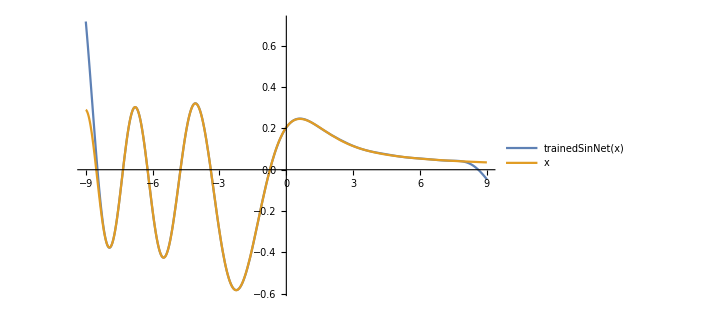

Abstract

GOAL OF THE PROJECT: To approximate mathematical functions using neural network.

SUMMARY OF WORK:.12 We have tried different neural network architectures to approximate various mathematical functions. We used different metrics to determine the best architecture for a particular type of function.

RESULTS AND FUTURE  WORK: Some of the functions that we tried had oscillatory components, for example the Bessel and Scorer functions. In our explorations we found out that such functions are best approximated by neural networks with a sinusoidal activation function. On the other hand rational polynomials are better approximated by neural networks with a soft exponential activation function. 
All the functions that we approximated here were functions of single variables. An obvious extension of this work is to design neural networks to approximate functions of multiple variables.
More importantly, the yet to be realized grander aim of this project was to solve differential equations. Future work would be geared towards achieving that aim.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

```mathematica
dataScorer = (# -> ScorerGi[#]) &@ RandomReal[{-8, 8}, 5000];
$refRangeSc = Range[-8, 8, 0.1];
$refValuesSc = ScorerGi[$refRangeSc];
sinNet = NetChain[{LinearLayer[30], Sin, LinearLayer[20], Sin, LinearLayer[1]}, "Input" -> "Real", "Output" ->  NetDecoder["Scalar"]];
plotData[points_,color_]:=ListLinePlot[points,PlotStyle->color,FrameTicks->False,PlotRangePadding->0.1,Frame->True,PlotRange->All]
plotSolution[net_,t_]:=Show[plotData[{$refValuesSc},GrayLevel[0.7]],plotData[net@$refRangeSc,Red]]
```

```mathematica
trainedSinNet=NetTrain[sinNet, dataScorer,Automatic,"TrainedNet", MaxTrainingRounds->Quantity[10, "Seconds"],TrainingProgressReporting->{plotSolution[#Net,#AbsoluteBatch]&,"Interval"->0.2}];
```

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

We obtained fairly accurate approximations of some special functions (Scorer, Bessel, Airy, Associated Laguerre) using multilayer neural networks with different activation functions.

Code

Provide one of:

https://github.com/monstergroup42/starthere/blob/master/Project/metric.nb

Written Content / Lesson Plans

Conclusions in Detail

The approximations closely matched the actual function within the range of the training dataset. But there were observable deviations near the boundaries of the training dataset. However the optimistic outcome is that this approach did give some reasonable approximations even when the built-in FunctionApproximations package failed to do so.

All Visualizations

Data Sources Links/References

Future Directions

Approximations of functions of multiple variables using neural networks.

Solving ordinary differential equations using neural networks.

Solving partial differential equations using neural networks.

Background Info Links/References

https://en.wikipedia.org/wiki/Universal_approximation_theorem

https://becominghuman.ai/neural-networks-for-solving-differential-equations-fa230ac5e04c

Keywords

Provide keywords as items

< keyword 1 >

< keyword 2 >

Other

Date

Last Modified: Monday, July 03, 2017

```mathematica
"Add Timestamp"
```